## Lesson

Create a dataset object:

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7,"z"->1|>}]
```

Convert dataset into normal lists and associations:

```mathematica
Normal[%]
```

{<|x→2,y→4,z→6|>,<|x→11,y→7,z→1|>}

Combine the elements of multiple associations

```mathematica
Catenate[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7,"z"->1|>}]
```

{2,4,6,11,7,1}

@* represents the composition of functions applied right-to-left:

```mathematica
(f@*g@*h)[x]
```

f[g[h[x]]]

/* represents the composition of functions applied left-to-right:

```mathematica
(h/*g/*f)[x]
```

f[g[h[x]]]

## Questions

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

Q1. Make a word cloud of the planets, with weights determined by their number of moons.

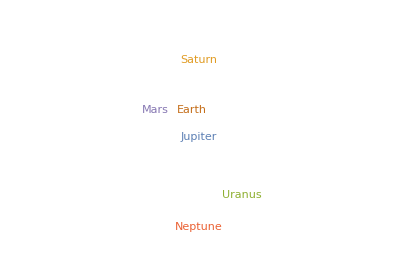

```mathematica
WordCloud[Normal[planets[All,"Moons",Length]]]
```

Q2. Make a bar chart of the number of moons for each planet.

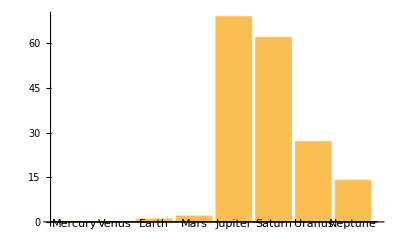

```mathematica
BarChart[planets[All,"Moons",Length],ChartLabels->Automatic]
```

Q3. Make a dataset of the masses of the planets, sorted by their number of moons.

```mathematica
planets[SortBy[Length[#Moons]&],"Mass"]
```

Q4. Make a dataset of planets and the mass of each one’s most massive moon.

```mathematica
planets[All,"Moons",Max,"Mass"]
```

Q5. Make a dataset of masses of planets, where the planets are sorted by the largest mass of their moons.

```mathematica
planets[SortBy[planets[All,"Moons",Max,"Mass"]],"Mass"]
```

Q6. Make a dataset of the median mass of all moons for each planet.

```mathematica
planets[All,"Moons",Median,"Mass"]
```

Q7. For each planet, make a list of moons larger in mass than 0.0001 Earth masses.

```mathematica
planets[All,"Moons",Select[#Mass>Quantity[1/10000,"EarthMass"]&]/*Keys]
```

Q8. Make a word cloud of countries in Central America, with the names of countries proportional to the lengths of the Wikipedia article about them.

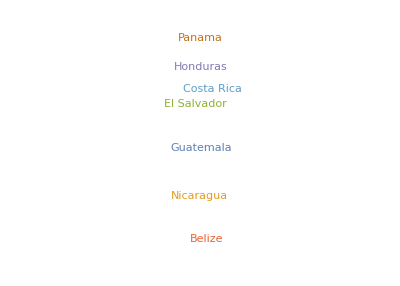

```mathematica
WordCloud[Association[#->StringLength[WikipediaData[#]]&/@CommonName[EntityList[EntityClass["Country","CentralAmerica"]]]]]
```

```mathematica
fireballs=ResourceData["Fireballs and Bolides"]
```

Q9. Find a dataset of the 5 largest observed altitudes in the Fireballs & Bolides dataset.

```mathematica
fireballs[Max,"Altitude"]
```

66.6 km

Q10. Find a dataset of the 5 largest observed altitudes in the Fireballs & Bolides dataset.

```mathematica
fireballs[TakeLargest[5],"Altitude"]
```

Q11. Make a histogram of the differences in successive peak brightness times in the Fireballs & Bolides dataset.

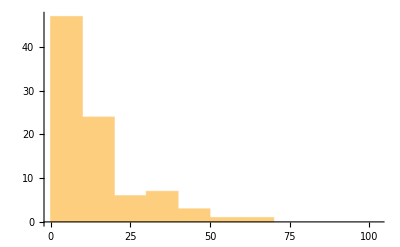

```mathematica
Histogram[Differences[Normal[ResourceData["Fireballs and Bolides"][All,"PeakBrightness"]]]]
```

Q12. Plot the nearest cities for the first 10 entries in the Fireballs & Bolides dataset, labeling each city.

```mathematica
GeoListPlot[fireballs[1;;10,"NearestCity"],GeoLabels->True]
```

-Graphics-

Q13. Plot the nearest cities for the 10 entries with largest altitudes in the Fireballs & Bolides dataset, labeling each city.

```mathematica
GeoListPlot[fireballs[TakeLargestBy[#Altitude&,10],"NearestCity"],GeoLabels->True]
```

-Graphics-